# Exporter Test

### Generate Graph and Association from Twine Project

#### Importer

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[twineImport]
twineImport[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,assocForm,edges,alledges, g, v},
fileAsString = Import[absoluteFilePath, "String"];
xmlObject = parseXML[fileAsString];
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
];
assocForm = Block[{passageContentWithLinks,completeAssociation},
(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentWithLinks= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Root Node Association*)
completeAssociation = <|rootNodeName -> passageContentWithLinks|>];
{completeGraph, assocForm}
]
twineImport::usage = "twineImport[path/to/file.html] gives a graph and an association of a Twine 2 project";
```

#### Exporter : Rewrite

```mathematica
Clear[twineExport]
twineExport[associationForm_Association, exportPathToFile_]:=Module[{storyAssoc = associationForm,twGraphVertices,twGraphPoints,sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
(*Grab Vertex Points for Passage Positions*)
twGraphVertices = GraphEmbedding[twineSummary[storyAssoc, "Graph"]];
Echo[twGraphVertices, "Graph Vertices "];
twGraphPoints = Reverse[Rescale[twGraphVertices,{-1,1}, {0, 250}]];
Echo[twGraphPoints, "Graph Points for Twine "];
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc = First[Values[storyAssoc]];
assocLength = Length[passageAssoc];
passages = Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"`xPos`,`yPos`\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧, "xPos" -> twGraphPoints⟦index⟧⟦1⟧, "yPos" -> twGraphPoints⟦index⟧⟦2⟧ |>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]
twineExport::usage = "twineExport[<| key1 → val1 ... |>, path/to/file] Exports WL Twine Representation to the specified path";
```

```mathematica
twineAssoc
```

<|TwineBridge_Test→<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>|>

```mathematica
twineAssoc["TwineBridge_Test"]["First Passage"]
```

This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?

```mathematica
Values[twineAssoc]//First
```

<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>

```mathematica
twineExport[twineAssoc, "~/Desktop/newForm-export-01"]
```

~/Desktop/newForm-export-01.html

#### Summarizer (Graph, Graph + Passage Display, Export)

```mathematica
Clear[twineSummary]
twineSummary[userAssoc_, outputForm_:"Summary"]:= Module[{firstEdge, passageEdges,psgContent,newPsgContent, buttonList,psgKeys,buttonGraph},
(*First Edge*)
firstEdge = {First[Keys[userAssoc]]-> Flatten[Keys[Values[userAssoc]]]⟦1⟧};

(*Passage Edges*)
passageEdges = Flatten@DeleteCases[Table[generateEdges[Flatten[Keys[Values[userAssoc]]]⟦index⟧, extractLinks[Flatten[Values[Values[userAssoc]]]⟦index⟧]], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}], {}];

(*Passage Content*)
psgContent = Table[generateEdges[Flatten[Keys[Values[userAssoc]]]⟦index⟧,Flatten[Values[Values[userAssoc]]]⟦index⟧], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}];

(*remove link syntax*)
newPsgContent = (psgContent /. DirectedEdge[id_,content_]:> DirectedEdge[id, StringReplace[content, ("[["~~ShortestMatch[p___]~~"]]"):> p]]);

(*List of Buttons*)
buttonList = newPsgContent/. DirectedEdge[name_, content_] :> Button[name, activePassage = content];

(*Get the Passage Keys*)
psgKeys = Flatten[Keys[Values[userAssoc]]];

(*Set the first Active Passage*)
activePassage = First[Keys[userAssoc]];

(*Replace the vertices of the graph with the buttons*)
buttonGraph = VertexReplace[Graph[Flatten[firstEdge~Join~passageEdges],], Table[psgKeys⟦i⟧ -> buttonList⟦i⟧, {i, Length[psgKeys]}]];
(*
 Summary ⇒ {Edges, Simple Graph} 
 Export  ⇒ Exports Story to TwineStories folder in current directory
*)

Switch[outputForm,
	"Summary", GraphicsRow[{Dynamic[Framed[activePassage]] , buttonGraph}],
	"Graph", buttonGraph,
	"Export",
		If[DirectoryQ[FileNameJoin[{NotebookDirectory[], "TwineStories"}]],
			Block[{twineFolder},
				twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
				twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
			],
			Block[{twineFolder},
				twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
				CreateDirectory[twineFolder];
				twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
				]
		];
	]
]
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>, \"Export\"] Exports WL Twine Representation to the TwineStories folder in the Current Notebook Directory";
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>] Displays the Twine Passages and the Graph";
```

### Import Twine Story

```mathematica
Clear[twineGraph, twineAssoc]
```

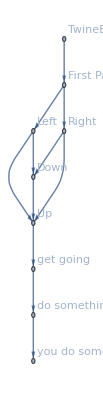
{-Graphics-,<|TwineBridge_Test→<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>|>}

```mathematica
{twineGraph, twineAssoc} =twineImport["~/Documents/Twine/Stories/TwineBridge_Test.html"]
```

### Different Forms

```mathematica
testingAssoc =<|"Other Story" -><|"Two" -> "Go to passage [[Three]]", "Three" ->  "Here we are at Passage Three"|>|>;
```

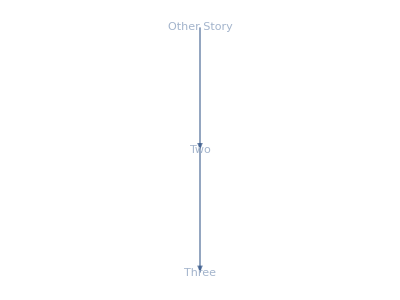

```mathematica
twineSummary[testingAssoc]
```

```mathematica
twineAssocNewForm = <|"TwineBridge_Test"-><|"First Passage"->"This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?","Left"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Right"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Up"->"Now that we are up why don&#39;t we [[get going]]?","Down"->"Now that we are down, why don&#39;t we get [[Up]]?","get going"->"Now that we are going, how about we [[do something]]","do something"->" Hi, I&#39;m doing something, why don&#39;t [[you do something]]?","you do something"->" Go, Get out of here! "|>|>;
```

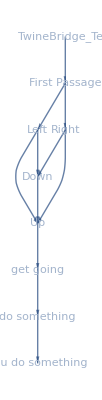

```mathematica
twineSummary[twineAssocNewForm]
```

```mathematica
twineSummary[twineAssocNewForm, "Graph"]
```

-Graphics-

```mathematica
twineSummary[twineAssocNewForm, "Export"]
```

Graph Vertices  {{0.,7.},{0.,6.},{-1.,5.},{0.,5.},{-1.,3.},{-1.,4.},{-1.,2.},{-1.,1.},{-1.,0.}}

Graph Points for Twine  {{0.,250.},{0.,500.},{0.,750.},{0.,1250.},{0.,1000.},{250.,1500.},{0.,1500.},{250.,1750.},{250.,2000.}}

The issue now: Need to LOCALIZE the Dynamic Variable, so for each story that is Summarized in a notebook the passages won’t interfere.

```mathematica
twineSummary[twineAssocNewForm, "Export"]
```

### Position of Passages

I can use the vertex positions from the graph for passage positions 
Let’s work on extracting those things.

```mathematica
Graph[{1,2, 3}, {1->2, 2->3,3 -> 1}]//GraphEmbedding
```

{{-0.866025,-0.5},{0.866025,-0.5},{1.83697×10^-16,1.}}

```mathematica
Rescale[%2562 , {Min[%2562], Max[%2562]}, {0, 100}]
```

{{0.,19.6152},{92.8203,19.6152},{46.4102,100.}}

```mathematica
GraphicsRow[{Column@GraphEmbedding@twineSummary[twineAssocNewForm, "Graph"],twineSummary[twineAssocNewForm, "Graph"] }]
```

```mathematica
Rescale[Rescale[%2573 ],{0,1}, {0,500}]
```

{{62.5,500.},{62.5,437.5},{0.,375.},{62.5,375.},{0.,250.},{0.,312.5},{0.,187.5},{0.,125.},{0.,62.5}}

```mathematica
Reverse/@%2619
```

{{500.,62.5},{437.5,62.5},{375.,0.},{375.,62.5},{250.,0.},{312.5,0.},{187.5,0.},{125.,0.},{62.5,0.}}

```mathematica
{{-1, 0}, {0, 0}, {1, 0}}
```

```mathematica
Transpose[{{-1, 0}, {0, 0}, {1, 0}}]
```

{{-1,0,1},{0,0,0}}

```mathematica
Rescale[#]&/@%2712
```

{{0,1/2,1},{0,0,0}}

```mathematica
Rescale[%2713, {0,1}, {10, 390}]
```

{{10,200,390},{10,10,10}}

```mathematica
Rescale[{{-1, 0}, {0, 0}, {1, 0}}, {-1, 1}, {10, 390}]
```

{{10,200},{200,200},{390,200}}

### isc405 Twine Story

```mathematica
{twISCGraph, twISCAssoc} =twineImport["~/Documents/Twine/Stories/isc405 _ Assignment 3.html"];
```

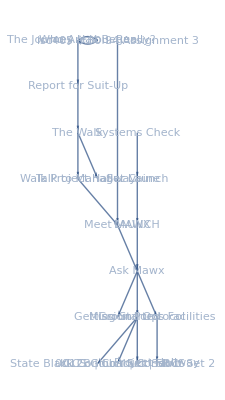

```mathematica
twineSummary[twISCAssoc]
```

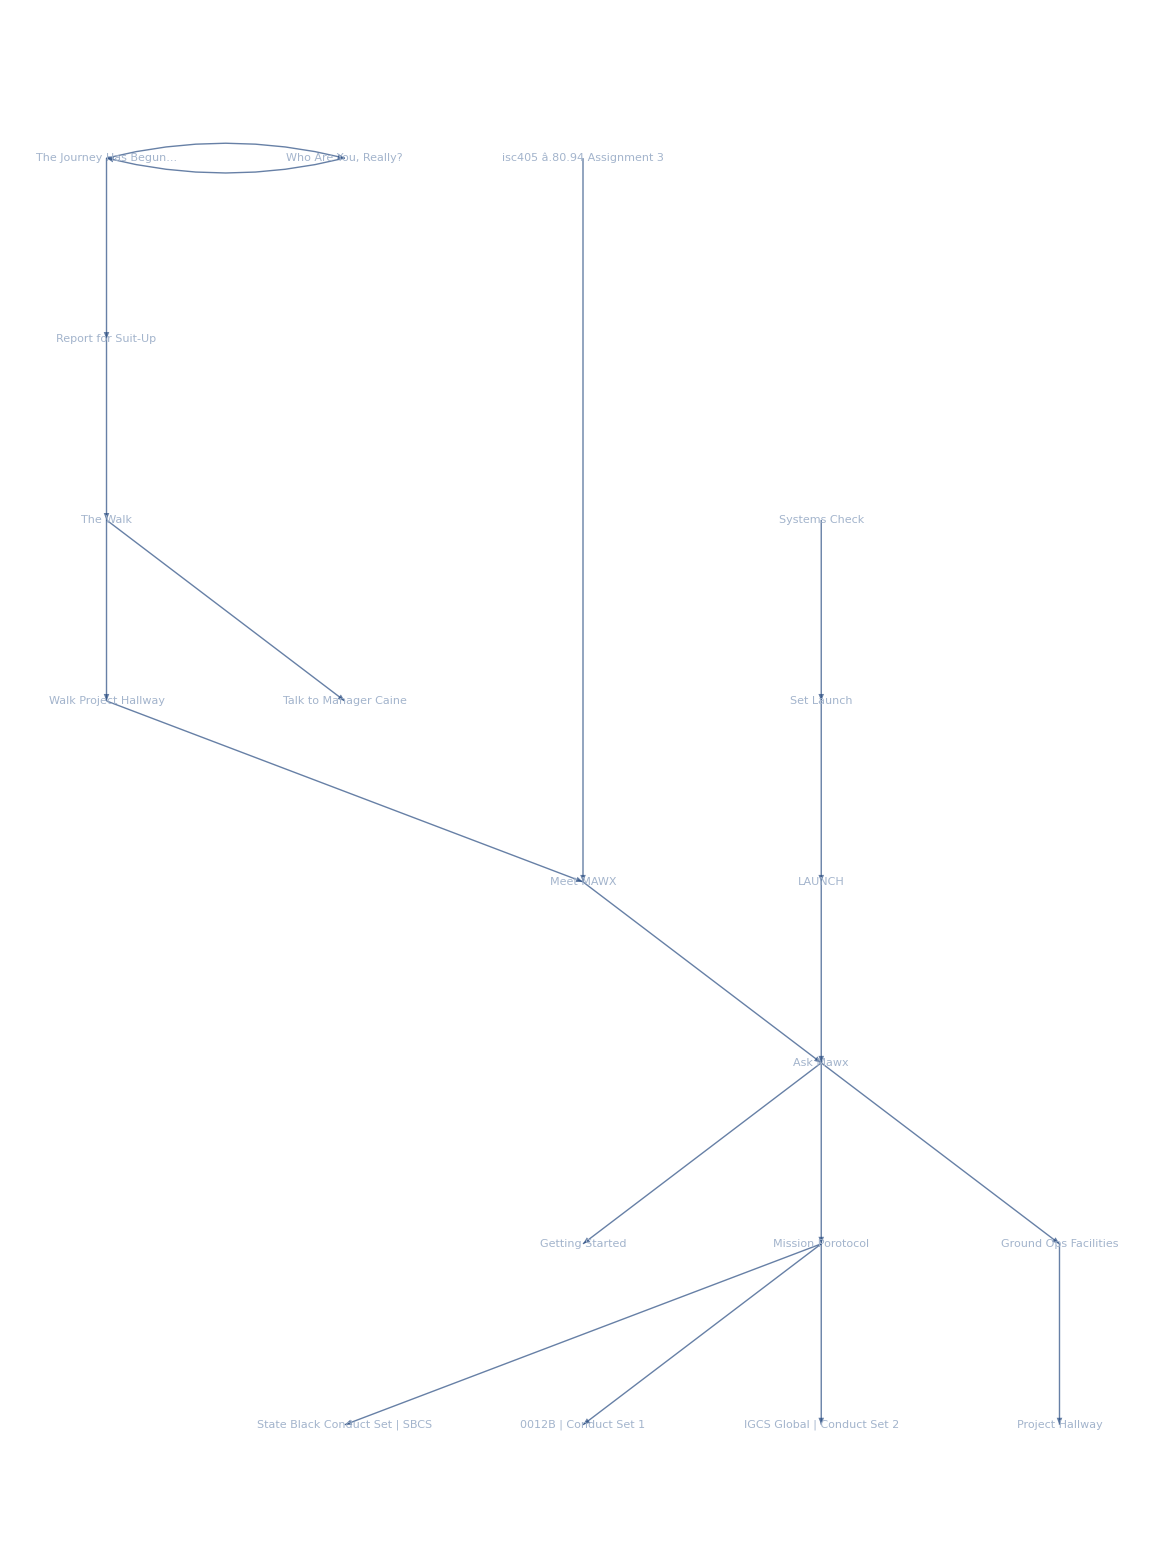

```mathematica
twineSummary[twISCAssoc, "Graph"]
```